Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

1 - 9 Integrals involving sine and cosine
Evaluate the following integrals.

1.∫_0^π 2/(k-Cos[θ])ⅆθ

```mathematica
Clear["Global`*"]
```

First I will search for singularities.

```mathematica
Reduce[k-Cos[θ]==0,{k,θ}]
```

C[1]∈Integers&&(θ==-ArcCos[k]+2 π C[1]||θ==ArcCos[k]+2 π C[1])

The cells both above and below show the pattern for multiples of ArcCos[k], and allow me to use simply ArcCos[k]+2 π as the root. However, looking at the interval of evaluation for the integral, only C[1]=0 will be available. For real k, this root will be on the x axis, constituting a simple pole, and that permits use of theorem 1 on p. 731.

The above mentioned theorem 1 sets forth the answer to the integral as

```mathematica
π ⅈ Residue[2/(k-Cos[θ]),{θ,ArcCos[k]}]
```

(2 ⅈ π)/(√(1-k^2))

Or,

```mathematica
(2 ⅈ π)/(√(1-k^2))==(2 ⅈ π)/(√(k^2-1)ⅈ)==(2  π)/(√(k^2-1))
```

3.  ∫_0^(2π) (1+Sin[θ])/(3+Cos[θ])ⅆθ

```mathematica
Clear["Global`*"]
```

```mathematica
Integrate[(1+Sin[θ])/(3+Cos[θ]),{θ,0,2 π}]
```

π/(√2)

I tried this a long way first, involving residue, but did not get the right answer. Just by pushing the integrate button, the right answer pops out.

5.  ∫_0^(2π) Cos[θ]^2/(5-4Cos[θ])ⅆθ

```mathematica
Clear["Global`*"]
```

```mathematica
Integrate[Cos[θ]^2/(5-4Cos[θ]),{θ,0,2 π}]
```

(5 π)/12

Another one matches the text answer without any preparation or application.

7.  ∫_0^(2π) a/(a-Sin[θ])ⅆθ

```mathematica
Clear["Global`*"]
```

```mathematica
Integrate[a/(a-Sin[θ]),{θ,0,2 π}]
```

```mathematica
2 √(a^2/(-1+a^2)) π==(2 √(a^2))/(√(1-a^2))π==(-2 a π)/(√(a^2-1))
```

Mathematica gives an answer with reversed sign, as compared to the text answer. (Mathematica took a long think on this.) Since this is the only problem in this section where there is disagreement in answers, I will attempt to work it out the long way.

```mathematica
∫_0^(2π) a/(a-Sin[θ])ⅆθ==a∫_0^(2π) 1/(a-Sin[θ])ⅆθ
```

True

Numbered line (2) on p. 726 has a way to modify the appearance of the denominator,

```mathematica
a-Sin[θ]==a-1/(2 ⅈ)(z-1/z)
```

and in the text below numbered line (2),

```mathematica
ⅆθ=ⅆz/(ⅈ z)
```

Implying that

```mathematica
∫_0^(2π) 1/(a-Sin[θ])ⅆθ==∮_C ⅆz/(ⅈ z(a-1/(2 ⅈ)(z-1/z)))
```

where C is the unit circle.

Operating on the denominator above,

```mathematica
ⅈ z(a-1/(2 ⅈ)(z-1/z))==ⅈ z a-(ⅈ z)/(2 ⅈ)z+1/(2 ⅈ)(ⅈ z)/z==ⅈ z a-z^2/2+1/2==-1/2(z^2-2 a ⅈ z-1)
```

making the last integral equal to

```mathematica
-2∮_C ⅆz/(z^2-2 a ⅈ z-1)
```

The denominator is a quadratic equation, with a=1, b=-2 a ⅈ , and c=-1. Solving,

```mathematica
Solve[z^2-2 a ⅈ z-1==0,z]
```

{{z→ⅈ a-√(1-a^2)},{z→ⅈ a+√(1-a^2)}}

The roots will be simple poles of the problem function.  A plot would be appropriate at this point.

```mathematica
p1=ParametricPlot[{1 Cos[t],1 Sin[t]},{t,-π,π},ImageSize->500,AxesLabel->{"Re","Im"},PlotRange->{-1.5,1.5},PlotStyle->{Thickness[0.004]},GridLines->Automatic];
```

```mathematica
p1p=ListPlot[Table[{Re[ⅈ a-√(1-a^2)],Im[ⅈ a-√(1-a^2)]},{a,-5,5}],PlotStyle->{Red}];
```

```mathematica
p2p=ListPlot[Table[{Re[ⅈ a+√(1-a^2)],Im[ⅈ a+√(1-a^2)]},{a,-5,5}],PlotStyle->{Blue}];
```

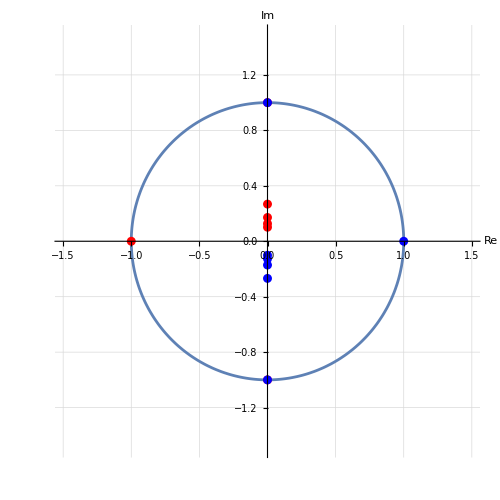

```mathematica
Show[p1,p1p,p2p]
```

There appear to be 8 points inside the unit circle. For the first table below (red points), these are n=2,3,4,5.

```mathematica
TableForm[Table[{a,N[Re[ⅈ a-√(1-a^2)]],N[Im[ⅈ a-√(1-a^2)]],Re[ⅈ a-√(1-a^2)],Im[ⅈ a-√(1-a^2)]},{a,-5,5}]]
```

-5 | 0. | -9.89898 | 0 | -5-2 √6
-4 | 0. | -7.87298 | 0 | -4-√15
-3 | 0. | -5.82843 | 0 | -3-2 √2
-2 | 0. | -3.73205 | 0 | -2-√3
-1 | 0. | -1. | 0 | -1
0 | -1. | 0. | -1 | 0
1 | 0. | 1. | 0 | 1
2 | 0. | 0.267949 | 0 | 2-√3
3 | 0. | 0.171573 | 0 | 3-2 √2
4 | 0. | 0.127017 | 0 | 4-√15
5 | 0. | 0.101021 | 0 | 5-2 √6

A series like the below may not be too smart, but it is possible.

```mathematica
Series[a/(a-Sin[θ]),{a,5-2 √6,4}]
```

Which I take to mean that I could examine residues in terms of a if I wanted to.

```mathematica
Residue[a/(a-Sin[θ]),{a,5-2 √6}]
```

0

```mathematica
Residue[a/(a-Sin[θ]),{a,4-2 √6}]
```

0

```mathematica
Residue[a/(a-Sin[θ]),{a,3-2 √2}]
```

0

```mathematica
Residue[a/(a-Sin[θ]),{a,2-√3}]
```

0

The cells above are probably an abuse of the Residue function. In any case, all are zero. Next are the blue points, n=-5,-4,-3,-2.

```mathematica
TableForm[Table[{a,N[Re[ⅈ a+√(1-a^2)]],N[Im[ⅈ a+√(1-a^2)]],Re[ⅈ a+√(1-a^2)],Im[ⅈ a+√(1-a^2)]},{a,-5,5}]]
```

-5 | 0. | -0.101021 | 0 | -5+2 √6
-4 | 0. | -0.127017 | 0 | -4+√15
-3 | 0. | -0.171573 | 0 | -3+2 √2
-2 | 0. | -0.267949 | 0 | -2+√3
-1 | 0. | -1. | 0 | -1
0 | 1. | 0. | 1 | 0
1 | 0. | 1. | 0 | 1
2 | 0. | 3.73205 | 0 | 2+√3
3 | 0. | 5.82843 | 0 | 3+2 √2
4 | 0. | 7.87298 | 0 | 4+√15
5 | 0. | 9.89898 | 0 | 5+2 √6

```mathematica
Residue[a/(a-Sin[θ]),{a,-5+2 √6}]
```

0

```mathematica
Residue[a/(a-Sin[θ]),{a,-4+√15}]
```

0

```mathematica
Residue[a/(a-Sin[θ]),{a,-3+2 √2}]
```

0

```mathematica
Residue[a/(a-Sin[θ]),{a,-2+√3}]
```

0

The residues of all the blue points also equal zero. What has been accomplished, at least, is to find eight values of a which, when inserted into the root formula, produce roots inside the unit circle. So returning to the problem function, I can ask for a table of a values, like so

```mathematica
TableForm[Table[{a,Integrate[a/(a-Sin[θ]),{θ,0,2 π}]},{a,{-5,-4,-3,-2,2,3,4,5}}]]
```

-5 | (5 π)/(√6)
-4 | (8 π)/(√15)
-3 | (3 π)/(√2)
-2 | (4 π)/(√3)
2 | (4 π)/(√3)
3 | (3 π)/(√2)
4 | (8 π)/(√15)
5 | (5 π)/(√6)

All of the resulting values conform to the text answer, (2 a π)/(√(a^2-1)), and these test cases carry a positive sign. Maybe this suggests that Mathematica’s answer was in error. In any case it is puzzling that no minus sign is generated when evaluating integer tokens, but a minus sign is generated when evaluating symbolic tokens. What if the integral is presented in a different way?

```mathematica
Integrate[a/(a-Sin[θ]),{θ,0,2 π},Assumptions->a∈ Integers]
```

ConditionalExpression[(2 a π Sign[a])/(√(-1+a^2)),Im[ArcSin[a]]≠0||Re[ArcSin[a]]>π||π+Re[ArcSin[a]]<0]

The numerator of the conditional expression is structured to remain positive. This could be used as a definitive result, but I’ll continue, next with a try at splitting up the integral into two pieces.

```mathematica
Integrate[a/(a-Sin[θ]),{θ,0,2 π},Assumptions->-5≤a≤-2]
```

-(2 a π)/(√(-1+a^2))

The above cell agrees with the test results for specific negative values of a.

```mathematica
Integrate[a/(a-Sin[θ]),{θ,0,2 π},Assumptions->2≤a≤5]
```

(2 a π)/(√(-1+a^2))

The above cell agrees with the test results for specific positive values of a. At this point it looks like Mathematica may have a better adapted solution, whereas the text answer may fail on blue points. (Checking again, I cannot see that negative values of a are prohibited.) The case may be better defined, but it is still a case of disagreement.

9.  ∫_0^(2π) Cos[θ]/(13-12Cos[2θ])ⅆθ

```mathematica
Clear["Global`*"]
```

```mathematica
Integrate[Cos[θ]/(13-12Cos[2θ]),{θ,0,2 π}]
```

0

10 - 22 Improper integrals: Infinite interval of integration
Evaluate the following integrals.

11.  ∫_(-∞)^∞ 1/((1+x^2)^2)ⅆx

```mathematica
Clear["Global`*"]
```

```mathematica
Integrate[1/((1+x^2)^2),{x,-∞,∞}]
```

π/2

13.  ∫_(-∞)^∞ x/((1+x^2)(x^2+4))ⅆx

```mathematica
Clear["Global`*"]
```

```mathematica
Integrate[x/((1+x^2)(x^2+4)),{x,-∞,∞}]
```

0

15.  ∫_(-∞)^∞ x^2/(x^6+1)ⅆx

```mathematica
Clear["Global`*"]
```

```mathematica
Integrate[x^2/(x^6+1),{x,-∞,∞}]
```

π/3

17.  ∫_(-∞)^∞ Sin[3 x]/(x^4+1)ⅆx

```mathematica
Clear["Global`*"]
```

```mathematica
∫_(-∞)^∞ Sin[3 x]/(x^4+1)ⅆx
```

0

19.  ∫_(-∞)^∞ 1/(x^4-1)ⅆx

```mathematica
Clear["Global`*"]
```

```mathematica
Integrate[1/(x^4-1),{x,-∞,∞},PrincipalValue->True]
```

-π/2

In this problem, I got a non-converge warning until I added the request for principal value.

21.  ∫_(-∞)^∞ Sin[x]/((x-1)(x^2+4))ⅆx

```mathematica
Clear["Global`*"]
```

```mathematica
Integrate[Sin[x]/((x-1)(x^2+4)),{x,-∞,∞},PrincipalValue->True]
```

1/5 π (-1/ⅇ^2+Cos[1])

In this problem, I got a non-converge warning until I added the request for principal value.

23 - 26 Improper integrals: Poles on the real axis
Find the Cauchy principal value.

23.  ∫_(-∞)^∞ 1/(x^4-1)ⅆx

```mathematica
Clear["Global`*"]
```

```mathematica
Integrate[1/(x^4-1),{x,-∞,∞},PrincipalValue->True]
```

-π/2

25.  ∫_(-∞)^∞ (x+5)/(x^3-x)ⅆx

```mathematica
Clear["Global`*"]
```

```mathematica
Integrate[(x+5)/(x^3-x),{x,-∞,∞},PrincipalValue->True]
```

0

All of the green cells in this section contain expressions which agree with the text answers.